## Naloga 3

Sestavite funkcijo naloga3[s_, p_], kot je zapisano v navodilih.

```mathematica
soda[{}]:={}
liha[{}]:={}
lump[{denar_,ime_}]:=denar<0
soda[l_List]:=Join[Reverse[First[l]],liha[Rest[l]]]
liha[l_List]:=Join[First[l],soda[Rest[l]]]
naloga3[s_,k_]:=Map[(#[[2]])&,Select[Transpose[{Differences[k],liha[s]}],lump]]
```

```mathematica
naloga3[{{"Jani","Tone","Cilka"},{"Ana","Franci","Boris"},{"Pero","Damir","Božo"},{"Jasna","Mojca","Aleš"}},
{0,5,6,12,7,11,20,10,12,12,12,15,13}]
```

{Boris,Pero,Jasna}

```mathematica
liha[{{"Jani","Tone","Cilka"},{"Boris","Franci","Ana"},{"Pero","Damir","Božo"},{"Jasna","Mojca","Aleš"}}]
```

{Jani,Tone,Cilka,Ana,Franci,Boris,Pero,Damir,Božo,Aleš,Mojca,Jasna}

```mathematica
N[GoldenRatio]
```

1.61803

## Naloga 4

Sestavite funkcijo naloga4[n_], kot je zapisano v navodilih.

```mathematica
Clear[naloga4,daljice2,daljice1]
daljice2[u_,d_,0]:={}
daljice1[u_,d_,0]:={}
daljice2[u_,d_,n_]:=With[{a=d+(u-d)*{0,1}*1/(1+GoldenRatio)},Append[daljice1[u,a,n-1],Line[{a,a+(d-u)*{-1,0}}]]]
daljice1[u_,d_,n_]:=With[{a=u+(d-u)*{1,0}*1/(1+GoldenRatio)},Append[daljice2[a,d,n-1],Line[{a,a+(d-u)*{0,1}}]]]
naloga4[n_]:=With[{u={0,0},d={2,1}},Graphics[{Line[{u,u+d*{1,0},u+d,u+d*{0,1},u}],daljice1[u,d,n]}]]
```

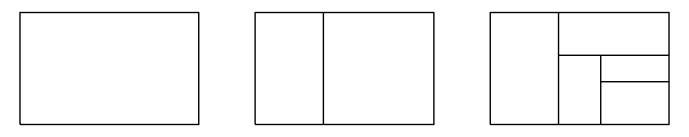

```mathematica
GraphicsRow[{naloga4[0],naloga4[1],naloga4[4]}]
```

```mathematica
?Export
```

RowBox[{"Export", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\).\!\(\*StyleBox[\"ext\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["expr", "TI"]}], "]"}] exports data to a file, converting it to the format corresponding to the file extension StyleBox["ext", "TI"]. 
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["\"\!\(\*StyleBox[\"format\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] exports data in the specified format.
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["exprs", "TI"], ",", StyleBox["elems", "TI"]}], "]"}] exports data by treating StyleBox["exprs", "TI"] as elements specified by StyleBox["elems", "TI"].